# B - spline curves

Dianne Hansford

## Demonstrate three knot sequences with varying knot multiplicities. Each curve has 4 domain intervals

```mathematica
(* all curves are degree 3 *)
n=3;  
(* all curves have the same number of domain intervals *)
ll = 4; 

fct[x_] := {Cos[x/2], Sin[x/2]};
fct2[x_] := {x, Sin[2*x]};

(* Each curve should use the same function !!! *)

knot1 = {0,0,0,0,1,2,3,4,4,4,4};
numk1 = Length[knot1];
numd1 = 6; (* number of deboor points -1 *)
dd1 = Table[fct2[x],{x,0,numd1}];

knot2 = {0,0,0,0,1,2,2,3,4,4,4,4};
numk2 = Length[knot2];
numd2 = 7; (* number of deboor points *)
dd2= Table[fct2[x],{x,0,numd2}];


knot3 = {0,0,0,0,1,2,2,2,3,4,4,4,4};
numk3 = Length[knot3];
numd3 = 8; (* number of deboor points *)
dd3 = Table[fct2[x],{x,0,numd3}];
```

```mathematica
(* curve evaluation *)
bsplinecurve[dd_,knot_,numd_,t_]:=Sum[BSplineBasis[{n,knot},i,t]*dd[[i+1]],{i,0,numd}];
```

```mathematica
(* Extract the juntion points *)
 
jpts1 = {
bsplinecurve[dd1,knot1,numd1,knot1[[4]]], bsplinecurve[dd1,knot1,numd1,knot1[[5]]],bsplinecurve[dd1,knot1,numd1,knot1[[6]]],bsplinecurve[dd1,knot1,numd1,knot1[[7]]],bsplinecurve[dd1,knot1,numd1,knot1[[8]]]};
 
jpts2 = {
bsplinecurve[dd2,knot2,numd2,knot2[[4]]], 
bsplinecurve[dd2,knot2,numd2,knot2[[5]]],
bsplinecurve[dd2,knot2,numd2,knot2[[6]]],
bsplinecurve[dd2,knot2,numd2,knot2[[8]]],
bsplinecurve[dd2,knot2,numd2,knot2[[9]]]};

jpts3 = {
bsplinecurve[dd3,knot3,numd3,knot3[[4]]], 
bsplinecurve[dd3,knot3,numd3,knot3[[5]]],
bsplinecurve[dd3,knot3,numd3,knot3[[6]]],
bsplinecurve[dd3,knot3,numd3,knot3[[9]]],
bsplinecurve[dd3,knot3,numd3,knot3[[10]]]};
```

## Plot All

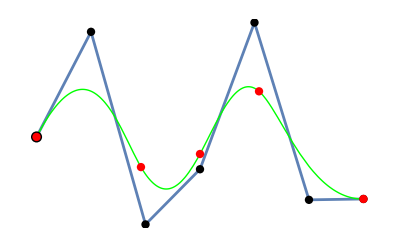

degree = 3  Number segments  = 4

knots1 = {0,0,0,0,1,2,3,4,4,4,4}

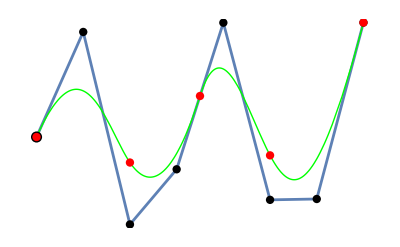

degree = 3  Number segments  = 4

knots2 = {0,0,0,0,1,2,2,3,4,4,4,4}

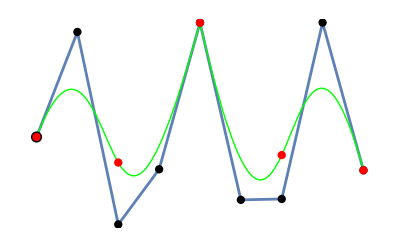

degree = 3  Number segments  = 4

knots3 = {0,0,0,0,1,2,2,2,3,4,4,4,4}

Show them in a row

All are degree 3 and 4 polynomial intervals

Knots from left to right

knots1=  {0,0,0,0,1,2,3,4,4,4,4}

knots2 = {0,0,0,0,1,2,2,3,4,4,4,4}

knots3 = {0,0,0,0,1,2,2,2,3,4,4,4,4}

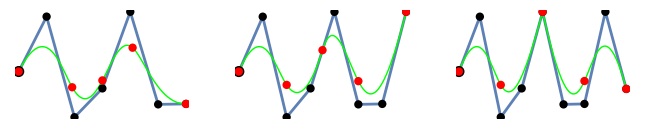

```mathematica
(* CURVE 1 *)
cplot1=ParametricPlot[bsplinecurve[dd1,knot1,numd1,t],{t,knot1[[n+1]],knot1[[numk1-n]]},PlotStyle->{Thick,Green}];
points1=Graphics[{Black,PointSize[0.015],Point[dd1],PointSize[0.02],Point[dd1[[1]]]}];
ddplot1=ListLinePlot[dd1];
jptsplot1 = Graphics[{Red,PointSize[0.015],Point[jpts1]}]; 
plot1 = Show[{ddplot1, cplot1,points1, jptsplot1},Axes-> False]

Print["degree = ",n,"  Number segments  = ",ll];
Print["knots1 = ",knot1];
(*Print["First deboor point larger"]; *)
(*Print["deboor points =",MatrixForm[dd1]];*)

(* CURVE 2 *)
cplot2=ParametricPlot[bsplinecurve[dd2,knot2,numd2,t],{t,knot2[[n+1]],knot2[[numk2-n]]},PlotStyle->{Thick,Green}];
points2=Graphics[{Black,PointSize[0.015],Point[dd2],PointSize[0.02],Point[dd2[[1]]]}];
ddplot2=ListLinePlot[dd2];
jptsplot2= Graphics[{Red,PointSize[0.015],Point[jpts2]}]; 
plot2 = Show[{ddplot2, cplot2,points2, jptsplot2},Axes-> False]

Print["degree = ",n,"  Number segments  = ",ll];
Print["knots2 = ",knot2];

(* CURVE 3 *)
cplot3=ParametricPlot[bsplinecurve[dd3,knot3,numd3,t],{t,knot3[[n+1]],knot3[[numk3-n]]},PlotStyle->{Thick,Green}];
points3=Graphics[{Black,PointSize[0.015],Point[dd3],PointSize[0.02],Point[dd3[[1]]]}];
ddplot3=ListLinePlot[dd3];
jptsplot3 = Graphics[{Red,PointSize[0.015],Point[jpts3]}]; 
plot3 = Show[{ddplot3, cplot3,points3, jptsplot3},Axes-> False]

Print["degree = ",n,"  Number segments  = ",ll];
Print["knots3 = ",knot3];

Print["  "];
Print["  "];
Print["Show them in a row"];
Print["All are degree 3 and 4 polynomial intervals "];
Print["Knots from left to right"];
Print["knots1=  ",knot1];
Print["knots2 = ",knot2];
Print["knots3 = ",knot3];

GraphicsRow[{plot1, plot2, plot3}]
```